### Example of use of “StateDiagrams.m”

#### Initialization

Loads the StateDiagrams.m package (change the directory to the folder you are using)

```mathematica
Directory[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"StateDiagrams_mma-v12.m"
```

A list of the available functions in the package is obtained by the command:

```mathematica
Names["Dependability`StateDiagrams`*"]
```

{ArrangeMatrix,DownTimeDensity,DownTimeDensityLaplace,GenHomogeneousSystem,KoutofN,KoutofNMode,KroenSum,LabelList,MDT,MergeStates,MTBF,MTFF,MTTF,MUT,ParallelMode,PlotDiagram,ProbStationary,ProbTransient,RelFunc,SeriesMode,SetDiagonal,StepPlot,UnAvailability}

Check syntax in the examples in task 1 below, and by ?UnAvailability, etc.. of mouseover.
-Graphics-

```mathematica
?MTTF
?MTFF
```

## Lab 4: Dependability modelling

## Students: August Heltne-Karlson and Erik Turøy Midtun

### System description

In  this  part  you  are  going  to  develop  an  analytic  model  with  the  objective  to  study  the  dependability  with respect to airport availability and time until reopening of a runway after a snowfall.

In the modelling of the airport in this assignment you need reliability block diagrams and Markov models [see Chapter 7 in the textbook].

### Task 1: Model of two plowing trucks [warm-up, 0%]

The  main purpose of this task is to apply the Mathematica add-on package “StateDiagrams.m” to obtain transient steady state probabilities, and metrics such as (un)availability, reliability, MTBF, etc.

The example is the part of the airport that consists of two plow trucks.  
The trucks might break down (intensity λ_1) and need to be repaired (intensity μ_1).  
If both trucks have failed, no plowing can be conducted and this sub-system is down (with huge consequences when it starts snowing of  cause).

Following the description of “Matrix form” in “Section 5.2.4 Steady state solution” (also presented in the lecture and in the lecture notes from Nov 3) of the textbook, we will get a set of equations on a matrix form. 
1.1. Define the system state variable(s) and corresponding events and make a Markov model of the trucks as described above.
1.2. Define the transition intensity matrix of the trucks
1.3. Define operation modus of the three states  (this means, available/unavailable,  up/down, working/failed)
1.4. Plot the diagram as defined - compare against the figure from 1.1 to check if you have implemented the model correctly (states, transitions, and intensities)
1.5. Determine the transient and steady state probabilities 
1.6. Obtain symbolical expressions for transient (U(t),R(t)) and steady state measures (U,MTFF,MTTF,MTBF)
1.7. Provide numerical values of the measures
1.8. Plot the transient and steady state unavailability as a function of t - what do you observe?

```mathematica
(*
1.1. Define the system state variable(s) and corresponding events and make a Markov model of the trucks as described above.
state = number of failed trucks, events are truck failures and repair 
*)
```

-Graphics-

```mathematica
(*
1.2. Define the transition intensity matrix of the trucks
*)
(* initialise an empty 3x3 matrix *) 
𝒬=Table[",",{3},{3}]; 
(* assign intensities to all transitions, null to non-transitions *) 
𝒬[[1,2]]=2 Subscript[λ, 1]; (* assign failure rate *)
𝒬[[1,3]]=0; (* non-transition *)
𝒬[[2,1]]=Subscript[μ, 1];(* assign repair rate *)
𝒬[[2,3]]=Subscript[λ, 1]; (* assign failure rate *)
𝒬[[3,1]]=0;(* non-transition *)
𝒬[[3,2]]=2 Subscript[μ, 1]; (* assign repair rate *)
Subscript[ℳ, 1]= SetDiagonal[Transpose[𝒬]];(* add the diagonal elements, see Sect 5.2.4 *)
Subscript[ℳ, 1]//MatrixForm  (* Print nicely on matrix form *)
```

(-2 λ_1 | μ_1 | 0
2 λ_1 | -λ_1-μ_1 | 2 μ_1
0 | λ_1 | -2 μ_1)

```mathematica
(*
1.3. Define operation modus of the three states (True=up/working, False=down/failed)
*)
Subscript[ℒ, 1]={"Ok 
[1]", "1 down
[2]", "Both down
[3]"}; (* labelling states - alternative to just 1,2,3 *)
Subscript[𝒲, 1]={True, True, False};
```

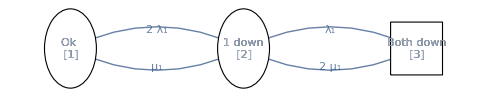

```mathematica
(*
1.4. Plot the diagram as defined - compare with figure above
*)
PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 1],Subscript[ℒ, 1]]
```

```mathematica
(*
1.5. Determine the transient and steady state probabilities 
*)
(* transient probabilities, defined a function of t *)
P[t_]:=ProbTransient[Subscript[ℳ, 1],{1,0,0},x] /. {x-> t}
(* show the funtion *)
P[t]
(* steady state probabilities *)
Subscript[PS, 1]=ProbStationary[Subscript[ℳ, 1]]
```

{(ⅇ^(-2 t (λ_1+μ_1)) (λ_1+ⅇ^(t (λ_1+μ_1)) μ_1)^2)/(λ_1+μ_1)^2,(2 ⅇ^(-2 t (λ_1+μ_1)) (-1+ⅇ^(t (λ_1+μ_1))) λ_1 (λ_1+ⅇ^(t (λ_1+μ_1)) μ_1))/(λ_1+μ_1)^2,((-1+ⅇ^(-t (λ_1+μ_1)))^2 λ_1^2)/(λ_1+μ_1)^2}

{μ_1^2/(λ_1+μ_1)^2,(2 λ_1 μ_1)/(λ_1+μ_1)^2,λ_1^2/(λ_1+μ_1)^2}

```mathematica
(*
1.6. Obtain symbolical expressions for transient (U(t),R(t)) and steady state measures (U,MTFF,MTTF,MTBF)
*)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,1] (* reliability function *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] (* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] (* Mean Time Between Failures *)
(* Unavailability, U(t), U *)
U[t_]:=UnAvailability[P[t],Subscript[𝒲, 1]] (* transient U(t) *)
U[t]
(*** Check assymptotic behaviour of U(t) when t->infinity ***)
Limit[U[t],{t-> Infinity}, Assumptions->Subscript[λ, 1]+Subscript[μ, 1]>0]
UnAvailability[Subscript[PS, 1],Subscript[𝒲, 1]] (* steady state *)
```

1/(2 (λ_1^2+6 λ_1 μ_1+μ_1^2))ⅇ^(-1/2 t (3 λ_1+μ_1+√(λ_1^2+6 λ_1 μ_1+μ_1^2))) ((1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) λ_1^2+μ_1 ((1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) μ_1+(-1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) √(λ_1^2+6 λ_1 μ_1+μ_1^2))+3 λ_1 (2 (1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) μ_1+(-1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) √(λ_1^2+6 λ_1 μ_1+μ_1^2)))

1/λ_1-(-λ_1-μ_1)/(2 λ_1^2)

((λ_1+μ_1) (4 λ_1+μ_1))/(2 λ_1^2 (2 λ_1+μ_1))

(λ_1+μ_1)^2/(2 λ_1^2 μ_1)

((-1+ⅇ^(-t (λ_1+μ_1)))^2 λ_1^2)/(λ_1+μ_1)^2

λ_1^2/(λ_1+μ_1)^2

λ_1^2/(λ_1+μ_1)^2

```mathematica
(*
1.7. Numerical values of the measures
Use these parameter sets 
*)
Subscript[𝒫, 11]= {Subscript[λ, 1]-> 0.1, Subscript[μ, 1]->1}
Subscript[𝒫, 12]= {Subscript[λ, 1]-> 0.5, Subscript[μ, 1]->1}

ProbStationary[Subscript[ℳ, 1]]/. Subscript[𝒫, 11] (* solve symbolically first -> then make numerical *)
ProbStationary[(Subscript[ℳ, 1] /. Subscript[𝒫, 11])] (* RECOMMENDED FOR LARGE MODELS: make matrix numerical first -> then solve *)

(* Subscript[𝒫, 11]= {Subscript[λ, 1]-> 0.1, Subscript[μ, 1]->1} *)
UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 11] (* transient *)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,0] /. Subscript[𝒫, 11] (* reliability function *)
UnAvailability[PS,Subscript[𝒲, 1]] /. Subscript[𝒫, 11](* steady state *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] /. Subscript[𝒫, 11](* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 11] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 11] (* Mean Time Between Failures *)

(* Subscript[𝒫, 12]= {Subscript[λ, 1]-> 0.5, Subscript[μ, 1]->1} *)
UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12] (* transient *)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,1] /. Subscript[𝒫, 12] (* reliability function *)
UnAvailability[PS,Subscript[𝒲, 1]] /. Subscript[𝒫, 12](* steady state *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] /. Subscript[𝒫, 12](* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 12] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 12] (* Mean Time Between Failures *)
```

{λ_1→0.1,μ_1→1}

{λ_1→0.5,μ_1→1}

{0.826446,0.165289,0.00826446}

{0.826446,0.165289,0.00826446}

0.00826446 (-1+ⅇ^(-1.1 t))^2

0.310559 ⅇ^(-1.28443 t) (1+ⅇ^(1.26886 t)+1.26886 (-1+ⅇ^(1.26886 t))+0.01 (1+ⅇ^(1.26886 t))+0.3 (1.26886 (-1+ⅇ^(1.26886 t))+2 (1+ⅇ^(1.26886 t))))

PS.{0,0,1}

65.

64.1667

60.5

0.111111 (-1+ⅇ^(-1.5 t))^2

0.117647 ⅇ^(-2.28078 t) (1+ⅇ^(2.06155 t)+2.06155 (-1+ⅇ^(2.06155 t))+0.25 (1+ⅇ^(2.06155 t))+1.5 (2.06155 (-1+ⅇ^(2.06155 t))+2 (1+ⅇ^(2.06155 t))))

PS.{0,0,1}

5.

4.5

4.5

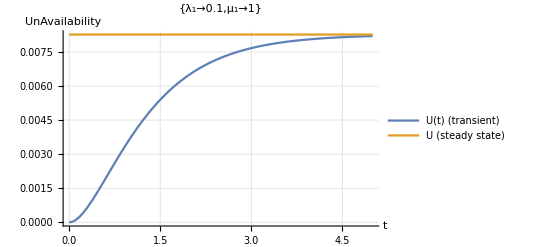

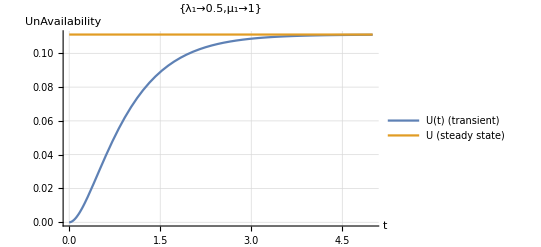

```mathematica
(* 
1.8. Plot the transient steady state unavailability as a function of t - what do you observe? 
*)
Plot[{
Legended[UnAvailability[P[t]/. Subscript[𝒫, 11],Subscript[𝒲, 1]],"U(t) (transient)"], 
Legended[UnAvailability[Subscript[PS, 1]/. Subscript[𝒫, 11],Subscript[𝒲, 1]],"U (steady state)"]},
{t,0,5},PlotRange->All, PlotLabel-> Subscript[𝒫, 11],AxesLabel->{Automatic,UnAvailability}, GridLines->Automatic]
Plot[{
Legended[UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12],"U(t) (transient)"], 
Legended[UnAvailability[Subscript[PS, 1],Subscript[𝒲, 1]]/. Subscript[𝒫, 12],"U (steady state)"]},
{t,0,5},PlotRange->All, PlotLabel-> Subscript[𝒫, 12],AxesLabel->{Automatic,UnAvailability}, GridLines->Automatic]
```

```mathematica
(* When to the unavailabilty exceed the tolerance level of 5%, using the set Subscript[𝒫, 12]? *)
FindRoot[(UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12])-0.05 == 0, {t,0.1}]
NSolve[(UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12])== 0.05 , t,Reals]
```

{t→0.740768}

{{t→-0.34221},{t→0.740768}}

### Task 2: Probability of open runways after snow fall [25%]

You are going to make a model to obtain the transient probability q_i(t) that  i runways are open at time t.  
Assume that 
- you have two runways, and that no trucks fail during plowing,  
- the expected snowing time is  1/κ  and plowing time is 1/γ,
- when both runways are cleaned and reopened, it is assumed that snowing stops
	(this means that we are only interested in the time until first reopening after the snow fall closed the airport), and
- two trucks can not plow the same runways simultaneously.

The objective is to study the transient period from closing both runways at t=0, and until the airport is partly (1 runway), and fully reopened (both runways).

2.1. Define the system state variable(s) and corresponding events and make a Markov model to obtain the transient state probabilities for n trucks.
The system state variables are  the number of available runways. The corresponding events are plowing the runways and snowing filling up the runways.
-Graphics-

{{-n γ_1,κ_1,0},{n γ_1,-γ_1-κ_1,0},{0,γ_1,0}}

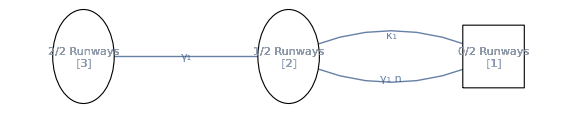

```mathematica
𝒬=Table[",",{3},{3}]; 
(* assign intensities to all transitions, null to non-transitions *) 
𝒬[[1,2]]=n*Subscript[γ, 1]; 
𝒬[[1,3]]=0; 
𝒬[[2,1]]=Subscript[κ, 1]; 
𝒬[[2,3]]=Subscript[γ, 1];
𝒬[[3,1]]=0;
𝒬[[3,2]]=0; 
Subscript[ℳ, 2]= SetDiagonal[Transpose[𝒬]];(* add the diagonal elements, see Sect 5.2.4 *)
 (* Print nicely on matrix form *)
Subscript[ℳ, 2]
Subscript[ℒ, 2]={
"0/2 Runways\n[1]", 
"1/2 Runways\n[2]",
"2/2 Runways\n[3]"}; 
Subscript[𝒲, 2]={False, True, True};  
PlotDiagram[Subscript[ℳ, 2],Subscript[𝒲, 2],Subscript[ℒ, 2]]
```

2.2. Use the package provided to obtain the probability q_i(t) that  i runways are reopened at time t, given that they were closed at t=0 after a heavy snow fall (general for n trucks).

```mathematica
P[t_]:=ProbTransient[Subscript[ℳ, 2],{1,0,0},x] /. {x-> t}
P[t] //Simplify;
For[i=0,i<3,i++,Print["q",i ,"=",Take[P[t],{i+1}]//Simplify]]
```

q0={1/(2 ((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (-1+n)^2 γ_1^2+κ_1 ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))+γ_1 (2 (1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (1+n) κ_1-(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (-1+n) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))}

q1={(ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) (-1+ⅇ^(t √(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) n γ_1)/(√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))}

q2={1/(2 (-4 n γ_1^2+((1+n) γ_1+κ_1)^2))ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) (-(1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) (-1+n)^2 γ_1^2-κ_1 ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-(1+n) γ_1 (2 (1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))}

2.3. Plot q_1(t) and q_2(t) for n=1 and n=2 and compare the results.  Use {γ→0.1,κ→1/60}[1/minutes]
	Plot all state probabilities for the first two hours (120 minutes) and discuss what you observe.  Use {γ→ 0.1,κ→ 1/60} [1/minutes]

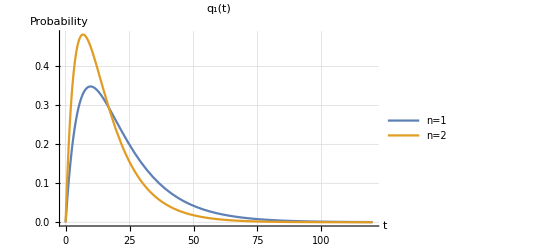

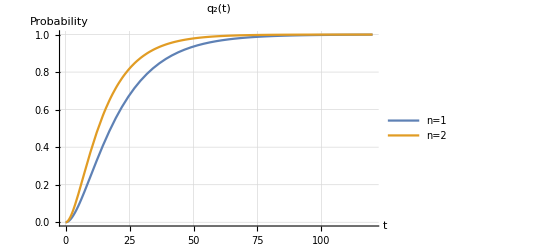

```mathematica
Subscript[𝒫, 11]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->1};
q0n1[t_]=Take[P[t],{1}]/. Subscript[𝒫, 11]//Simplify;
q1n1[t_]=Take[P[t],{2}]/. Subscript[𝒫, 11]//Simplify;
q2n1[t_]=Take[P[t],{3}]/. Subscript[𝒫, 11]//Simplify;

Subscript[𝒫, 12]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->2};
q0n2[t_]=Take[P[t],{1}]/. Subscript[𝒫, 12]//Simplify;
q1n2[t_]=Take[P[t],{2}]/. Subscript[𝒫, 12]//Simplify;
q2n2[t_]=Take[P[t],{3}]/. Subscript[𝒫, 12]//Simplify;

Plot[{
Legended[q1n1[t],"n=1"],
Legended[q1n2[t],"n=2"]},
{t,0,120},PlotRange->All, PlotLabel-> "q_1(t)",AxesLabel->{Automatic, "Probability"}, GridLines->Automatic]

Plot[{
Legended[q2n1[t],"n=1"],
Legended[q2n2[t],"n=2"]},
{t,0,120},PlotRange->All, PlotLabel-> "q_2(t)",AxesLabel->{Automatic,"Probability"}, GridLines->Automatic]
```

With (n=2) two plow trucks we see that in the beginning the probability of being in state 1, the state with no runways available, is lower than in the case with only one truck. We also see that with two trucks we get to the steady state(100% probability for both runways available) faster than with one truck. The overall availability is thus higher with two trucks.

Furthermore, find the maximum reopening time T_max for which the probability is ≥0.95,  P(T<T_max)≥0.95.
	  Compare n=1 and n=2.

```mathematica
Print["n=1"]
FindRoot[(q2n1[t])-0.95 == 0, {t,0.1}] 
Print["n=2"]
FindRoot[(q2n2[t])-0.95 == 0, {t,0.1}]
```

n=1

{t→53.6765}

n=2

{t→39.8451}

2.4. Compare the expected time until first reopening with n=1 and n=2. 
	Plot the relative difference in the expected time until first reopening (gain) for n=1 and n=2 as the expected snowing time 1/κ changes.

10-100 (-1/10-κ_1)

10-50 (-1/10-κ_1)

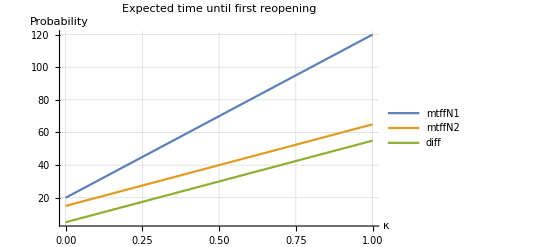

```mathematica
Subscript[𝒫, n1]= {n->1};
Subscript[𝒫, n2]= {n->2};
Subscript[𝒫, 24]= {Subscript[γ, 1]-> 1/10};
Subscript[𝒲, 24]={True,True, False};  
mtffN1=MTFF[Subscript[ℳ, 2],Subscript[𝒲, 24]] /. Subscript[𝒫, n1] /. Subscript[𝒫, 24] 
mtffN2=MTFF[Subscript[ℳ, 2],Subscript[𝒲, 24]] /. Subscript[𝒫, n2] /. Subscript[𝒫, 24] 
mtffN21[k_] :=mtffN1  /.{Subscript[κ, 1]-> k}
mtffN22[k_] :=mtffN2  /.{Subscript[κ, 1]-> k}
diff [k_] := mtffN1 -mtffN2 /.{Subscript[κ, 1]-> k}

Plot[{
Legended[mtffN21[κ],"mtffN1"],
Legended[mtffN22[κ],"mtffN2"],
Legended[diff[κ],"diff"]},
{κ,0,1},PlotRange->All, PlotLabel-> "Expected time until first reopening",AxesLabel->{Automatic,"Probability"}, GridLines->Automatic]
```

Discuss the gain you get by adding one truck (n=1 -> n=2) when κ changes. Use {γ→0.1} [1/minutes] 
Text
	
	What is the minimum and maximum gain (and for which κ value)?
Text

### Task 3: Two plowing trucks with two repairmen who might go on sick-leave [30%]

The repair of the trucks depends on a repairman.  
In the model from task 1 we assumed that we have one repairman per truck.  
However, the repairmen might get sick (intensity ν) and are recovered (intensity ϵ).  
Make the necessary changes in the model from task 1 to take into account that the repair of a truck might get delayed due to (a) sick repairman(men). 

3.1. Define the system state variable(s) and corresponding events, and make a Markov model to obtain state probabilities.
-Graphics-
1 2 3
4 5 6
7 8 9

```mathematica
Subscript[Q, 3]= {
{, 2λ,0,2ν,0,    0,      0,0,  0},
{μ,,   λ, 0,     2ν,0,     0,0,  0},
{0,2μ,, 0,     0,     2ν,0,0,  0},
{ϵ,0,  0, ,     2λ,   0,      ν,0,  0},
{0,ϵ,  0, μ,     ,      λ,      0,ν,  0},
{0,0,  ϵ, 0,     μ,      ,      0,0,  ν},
{0,0,  0, 2ϵ, 0,      0,      ,2λ,0},
{0,0,  0, 0,      2ϵ, 0,      0,,   λ},
{0,0, 0,  0,     0,      2ϵ,  0,0,   }
} ;
Subscript[ℳ, 3]=SetDiagonal[Transpose[Subscript[Q, 3]]];
(*Subscript[Q, 32]={
{0, μ,0,ϵ,0,0,0,0,0},
{2λ, 0,2μ,0,ϵ,0,0,0,0},
{0, λ,0,0,0,ϵ,0,0,0},
{2*v, 0,0,0,μ,0,2ϵ,0,0},
{0, 2*v,0,2λ,0,μ,0,2ϵ,0},
{0, 0,2*v,0,λ,0,0,0,2ϵ},
{0, 0,0,v,0,0,0,0,0},
{0, 0,0,0,v,0,2λ,0,0},
{0, 0,0,0,0,v,0,λ,0}
} ;*)
Subscript[ℒ, 3]={"1","2","3", "4", "5", "6","7","8","9"}; 
Subscript[𝒲, 3]={True, True, False, True, True, False, True, True, False};  
PlotDiagram[Subscript[ℳ, 3],Subscript[𝒲, 3],Subscript[ℒ, 3]]
(*PlotDiagram[Subscript[Q, 32] ,Subscript[𝒲, 3],Subscript[ℒ, 3]]*)
```

```mathematica
P[t_]:=ProbTransient[Subscript[ℳ, 3],{1,0,0,0,0,0,0,0,0},x] /. {x-> t}
```

3.2. Use the package provided to obtain the probability that n=0, 1, and 2 trucks are available for 𝒫_2={λ_2→0.1, μ_2 → 1, ν→ 0.01, ϵ →0.5}[1/days]

```mathematica
Subscript[𝒫, 2]={λ->0.1, μ -> 1, ν-> 0.01, ϵ ->0.5}
UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 11] (* transient *)
```

code

3.3. Compare the two models, without (task 1) and with (task 2) repairmen on sick leave with respect to the unavailability and the probability that one truck has failed. 
Change the repair intensity β (assume it partly depends on the skills) and discuss whether it is sufficient to have one truck or if you need two.  
You first need to define what you think is the maximum acceptable probability of not having a truck available.

```mathematica
code
```

code

3.4. Obtain the mean time to first failure, and mean time to failure.  Are they the same or different? Why?

```mathematica
code
```

code

text

### Task 4: Performability [15%] [no assistance]

The focus in this task is on what is called Performability - “a measurement of how a degradable system performs” [1],[2][3].  
In a performability model you combine the dependability model (here: truck availability model from task 3) with the performance (here: probability of reopening runways from task 2).
Let’s set the guaranteed maximum time to reopen to T_max=45 minutes.  

4.1. What is the probability P(T<T_max) that it takes less than T_max=45 minutes to reopen both runways?  
Calculate it for n=0, 1 and 2 trucks and using  {γ→ 0.1,κ→ 1/60} [1/minutes] from task 2.
4.2. Combine the probabilities (which are conditioned on n=0,1, and 2) with the model for truck availability from task 3 to obtain the overall probability that it takes less than T_max=45 minutes to reopen both runways.  
Use 𝒫_2={λ_2→0.1, μ_2 → 1, ν→ 0.01, ϵ →0.5} in the truck availability model.
4.3. Which factors contributes to the reopening time?  
Discuss what you would have done if you were asked to reduce the  guaranteed maximum time to reopen to T_max=30 minutes, without changing the guaranteed probability P(T<T_max). 
Calculate the new probabilities first, identify the factors that contributes, and do a qualitative discussions about (counter)measures that could be taken to ensure that the guaranteed probability P(T<T_max) is provided.

### Task 5: Structural model of the whole airport [30%] [no assistance]

The system is “up/working” when 
	- both runways, AND
	- at least 6 of 10 gates, AND
	- one of two deicing stations 
are available.

5.1. What do you have to assume to use a Reliability Block Diagram (RBD)?  What does this mean in the context of the airport system? Is this realistic? 
5.2. Make an Reliability Block Diagram (RBD) of the total airport system
5.3. Make reliability functions for 
	- R(t,λ) (single component), 
	- R_s(t,n,λ), for an n-serial structure 
	- R_p(t,n,λ), for an n-parallel structure 
	- R_kofn(t,k,n,λ), for a k-of-n structure
	Check function  by 
	Integrate[R_kofn[t,6, 10, λ],{t,0,∞}, Assumptions→λ>0]= 121/(360 λ). Which property have you now calculated?
	Explain how R_s(t,n,λ) and R_p(t,n,λ) can be replaced by R_kofn(t,k,n,λ).
	Plot R_kofn(t,6,10,λ) and R_kofn(t,8,10,λ) for 20 valued of λ in [1,20] (hint: use Table and ListPlot)
5.4. Use your reliability functions to determine the R_tot(t) for the airport, compliant with your RBD.
5.5. Plot R_tot(t) for  𝒫_λ={λ_1→ 0.02,λ_2→ 0.06,λ_3→ 0.1}[1/days]
	What is the probability that the airport runs without interruptions for 1 day, 1 week, and 1 month (including night shifts)?
5.6. What is the main cause of failure?  Which change(s) will have the highest effect?